## Rouse Eigenbasis

```mathematica
v[p_,n_,N_]:=If[p==0,√1/N,√2/N Cos[(n-1/2)(p*π)/N]]
V[N_]:=Table[v[p,n,N],{p,0,N-1},{n,N}]
```

## Average DSB Laplacian Matrix

Only the first monomer of the two-DSB cluster is random, uniformly distributed over all the allowed region ℓ which is defined naturally by N and g.

```mathematica
ℓ[N_,g_]:=N-g-3
𝒸[m_,N_,g_]:=Piecewise[{{4,Abs[m-(N+1)/2]≤(N-1)/2-g-3},{3,Abs[m-(N+1)/2]==(N-1)/2-g-2},{2,Abs[m-(N+1)/2]≤ (N-1)/2-1},{1,Abs[m-(N+1)/2]==(N-1)/2}}]
```

The probability of being broken is, for each monomer:

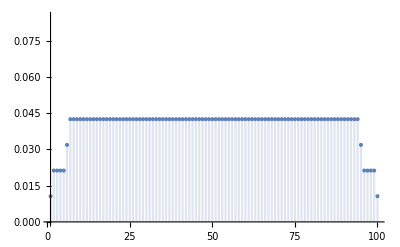

```mathematica
DiscretePlot[𝒸[m,100,3]/ℓ[100,3],{m,1,100}]
```

In effect, the expected number of broken monomers corresponds with the actual number of broken monomers (4):

```mathematica
∑_(m=1)^100 𝒸[m,100,3]/ℓ[100,3]
```

4

Finally, the average DSB Laplacian Matrix ⟨X⟩ is:

```mathematica
Xoff[N_,g_]:= SparseArray[{{i_,j_}:>-𝒸[i,N,g]/;Abs[i-j]==1},{N,N}]
X[N_,g_]:=1/(N-g-3)*(Xoff[N,g]-DiagonalMatrix[Total[Xoff[N,g],{2}]])
```

```mathematica
MatrixForm[X[30,4]]
```

(1/23 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/23 | 1/23)

## Eigenvalues of the average DSB Laplacian matrix

We compute the pseudo-diagonal matrix using the Rouse eigenbasis

```mathematica
pseudoDiagX[N_,g_]:=V[N].X[N,g].Transpose[V[N]]
```

```mathematica
ListPlot3D[pseudoDiagX[50,10],PlotRange->Full]
```

-Graphics3D-

We compare the diagonal of V.,⟨X⟩.V^T with the real (numerically computed) eigenvalues of ⟨X⟩.

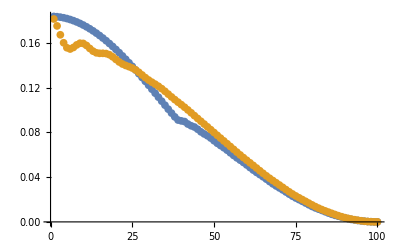

```mathematica
ListPlot[{Eigenvalues[X[100,10]],Reverse[Diagonal[pseudoDiagX[100,10]]]}]
```

⟨X⟩(g) can also be written as D_g M where M is the Rouse matrix and

```mathematica
Dg[N_,g_]:=SparseArray[{{i_,j_}:>𝒸[i,N,g]/;i==j},{N,N}]
```

For instance:

```mathematica
Dg[15,3] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Since V.,⟨X⟩.V^T = V.,D_g.M.V^T=V.,D_g.V^T.V.M.V^T=V.,D_g.V^T.Λ. and V.,D_g.V^T has a dominant diagonal,
 the diagonal elements of V.,⟨X⟩.V^T are almost equal to ω_p λ_p where ω_p are the diagonal elements of V.,D_g.V^T (perturbation) and λ_p are the Rouse eigenvalues.

```mathematica
TrigReduce[V[15].Dg[15,3].Transpose[V[15]]] // MatrixForm
```

(12/5 | 0 | 2/15 (√2 Cos[π/15]-4 √2 Cos[(2 π)/15]+2 √2 Sin[π/30]-3 √2 Sin[(7 π)/30]) | 0 | -2/15 (2 √2 Cos[π/15]-√2 Cos[(2 π)/15]+3 √2 Sin[π/30]-4 √2 Sin[(7 π)/30]) | 0 | -(8 √2)/15+4/15 √2 (1-√5)+1/5 √2 (1+√5) | 0 | -2/15 (3 √2 Cos[π/15]-2 √2 Cos[(2 π)/15]+4 √2 Sin[π/30]-√2 Sin[(7 π)/30]) | 0 | 0 | 0 | (8 √2)/15+4/15 √2 (-1-√5)+1/5 √2 (-1+√5) | 0 | 2/15 (4 √2 Cos[π/15]-3 √2 Cos[(2 π)/15]+√2 Sin[π/30]-2 √2 Sin[(7 π)/30])
0 | 2/15 (18+Cos[π/15]-4 Cos[(2 π)/15]+2 Sin[π/30]-3 Sin[(7 π)/30]) | 0 | 1/15 (√(2 (5+√5)) Cos[π/30]-2 √(2 (5-√5)) Cos[(7 π)/30]-4 √(2 (5-√5)) Sin[π/15]-3 √(2 (5+√5)) Sin[(2 π)/15]) | 0 | 2/15 (-3+√3 Cos[π/30]-2 √3 Cos[(7 π)/30]+4 √3 Sin[π/15]+3 √3 Sin[(2 π)/15]) | 0 | 1/15 (-1-√5-6 Cos[π/15]+4 Cos[(2 π)/15]-8 Sin[π/30]+2 Sin[(7 π)/30]) | 0 | 1/15 (-10+√(2 (5-√5)) Cos[π/30]+2 √(2 (5+√5)) Cos[(7 π)/30]+4 √(2 (5+√5)) Sin[π/15]-3 √(2 (5-√5)) Sin[(2 π)/15]) | 0 | 1/15 (1-√5) | 0 | 1/15 (1-√5+8 Cos[π/15]-6 Cos[(2 π)/15]+2 Sin[π/30]-4 Sin[(7 π)/30]) | 0
2/15 (√2 Cos[π/15]-4 √2 Cos[(2 π)/15]+2 √2 Sin[π/30]-3 √2 Sin[(7 π)/30]) | 0 | -2/15 (-18+2 Cos[π/15]-Cos[(2 π)/15]+3 Sin[π/30]-4 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5+2 Cos[π/15]-8 Cos[(2 π)/15]+4 Sin[π/30]-6 Sin[(7 π)/30]) | 0 | 1/15 (Cos[π/15]+√5 Cos[π/15]-4 Cos[(2 π)/15]+4 √5 Cos[(2 π)/15]+2 Sin[π/30]-2 √5 Sin[π/30]-3 Sin[(7 π)/30]-3 √5 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5) | 0 | 2/15 (3+Cos[π/15]-4 Cos[(2 π)/15]+2 Sin[π/30]-3 Sin[(7 π)/30]) | 0 | 1/15 (-10-Cos[π/15]+√5 Cos[π/15]+4 Cos[(2 π)/15]+4 √5 Cos[(2 π)/15]-2 Sin[π/30]-2 √5 Sin[π/30]+3 Sin[(7 π)/30]-3 √5 Sin[(7 π)/30]) | 0 | 1/15 (1-√5-8 Cos[π/15]+6 Cos[(2 π)/15]-2 Sin[π/30]+4 Sin[(7 π)/30])
0 | 1/15 (√(2 (5+√5)) Cos[π/30]-2 √(2 (5-√5)) Cos[(7 π)/30]-4 √(2 (5-√5)) Sin[π/15]-3 √(2 (5+√5)) Sin[(2 π)/15]) | 0 | 32/15 (5/8-(√5)/8)+8/5 (5/8+(√5)/8) | 0 | -4/5 √(1/3 (5/8-(√5)/8))+2/5 √(1/3 (5/8+(√5)/8))-2/5 √(3 (5/8+(√5)/8)) | 0 | 1/15 (-10+4 √(2 (5-√5)) Cos[π/30]+√(2 (5+√5)) Cos[(7 π)/30]+3 √(2 (5+√5)) Sin[π/15]-2 √(2 (5-√5)) Sin[(2 π)/15]) | 0 | -8/15 √((5/8-(√5)/8) (5/8+(√5)/8)) | 0 | 1/15 (-3 √(2 (5+√5)) Cos[π/30]+4 √(2 (5-√5)) Cos[(7 π)/30]+2 √(2 (5-√5)) Sin[π/15]+√(2 (5+√5)) Sin[(2 π)/15]) | 0 | 1/15 (-10+2 √(2 (5-√5)) Cos[π/30]+3 √(2 (5+√5)) Cos[(7 π)/30]+√(2 (5+√5)) Sin[π/15]-4 √(2 (5-√5)) Sin[(2 π)/15]) | 0
-2/15 (2 √2 Cos[π/15]-√2 Cos[(2 π)/15]+3 √2 Sin[π/30]-4 √2 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5+2 Cos[π/15]-8 Cos[(2 π)/15]+4 Sin[π/30]-6 Sin[(7 π)/30]) | 0 | -2/15 (-18+3 Cos[π/15]-2 Cos[(2 π)/15]+4 Sin[π/30]-Sin[(7 π)/30]) | 0 | 1/15 (-10-2 Cos[π/15]+2 √5 Cos[π/15]+Cos[(2 π)/15]+√5 Cos[(2 π)/15]-3 Sin[π/30]-3 √5 Sin[π/30]+4 Sin[(7 π)/30]-4 √5 Sin[(7 π)/30]) | 0 | 1/15 (1-√5-4 Cos[π/15]+2 Cos[(2 π)/15]-6 Sin[π/30]+8 Sin[(7 π)/30]) | 0 | -2/15 (3+2 Cos[π/15]-Cos[(2 π)/15]+3 Sin[π/30]-4 Sin[(7 π)/30]) | 0 | 1/15 (2 Cos[π/15]+2 √5 Cos[π/15]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+3 Sin[π/30]-3 √5 Sin[π/30]-4 Sin[(7 π)/30]-4 √5 Sin[(7 π)/30]) | 0 | 1/15 (-1+√5)
0 | 2/15 (-3+√3 Cos[π/30]-2 √3 Cos[(7 π)/30]+4 √3 Sin[π/15]+3 √3 Sin[(2 π)/15]) | 0 | -4/5 √(1/3 (5/8-(√5)/8))+2/5 √(1/3 (5/8+(√5)/8))-2/5 √(3 (5/8+(√5)/8)) | 0 | 12/5 | 0 | -2/15 (-3+4 √3 Cos[π/30]-√3 Cos[(7 π)/30]+3 √3 Sin[π/15]+2 √3 Sin[(2 π)/15]) | 0 | 2/5 √(1/3 (5/8-(√5)/8))-2/5 √(3 (5/8-(√5)/8))+4/5 √(1/3 (5/8+(√5)/8)) | 0 | 2/15 (-3+3 √3 Cos[π/30]-4 √3 Cos[(7 π)/30]+2 √3 Sin[π/15]+√3 Sin[(2 π)/15]) | 0 | 2/15 (-3+2 √3 Cos[π/30]-3 √3 Cos[(7 π)/30]+√3 Sin[π/15]+4 √3 Sin[(2 π)/15]) | 0
-(8 √2)/15+4/15 √2 (1-√5)+1/5 √2 (1+√5) | 0 | 1/15 (Cos[π/15]+√5 Cos[π/15]-4 Cos[(2 π)/15]+4 √5 Cos[(2 π)/15]+2 Sin[π/30]-2 √5 Sin[π/30]-3 Sin[(7 π)/30]-3 √5 Sin[(7 π)/30]) | 0 | 1/15 (-10-2 Cos[π/15]+2 √5 Cos[π/15]+Cos[(2 π)/15]+√5 Cos[(2 π)/15]-3 Sin[π/30]-3 √5 Sin[π/30]+4 Sin[(7 π)/30]-4 √5 Sin[(7 π)/30]) | 0 | 16/15+2/15 (1-√5)^2+1/10 (1+√5)^2 | 0 | 1/15 (-3 Cos[π/15]-3 √5 Cos[π/15]+2 Cos[(2 π)/15]-2 √5 Cos[(2 π)/15]-4 Sin[π/30]+4 √5 Sin[π/30]+Sin[(7 π)/30]+√5 Sin[(7 π)/30]) | 0 | 4/15+2/15 (-1-√5)+1/5 (1-√5)+2/15 (-1+√5)+2/15 (1+√5) | 0 | -16/15+2/15 (-1-√5) (1-√5)+1/10 (-1+√5) (1+√5) | 0 | 1/15 (10+4 Cos[π/15]-4 √5 Cos[π/15]-3 Cos[(2 π)/15]-3 √5 Cos[(2 π)/15]+Sin[π/30]+√5 Sin[π/30]-2 Sin[(7 π)/30]+2 √5 Sin[(7 π)/30])
0 | 1/15 (-1-√5-6 Cos[π/15]+4 Cos[(2 π)/15]-8 Sin[π/30]+2 Sin[(7 π)/30]) | 0 | 1/15 (-10+4 √(2 (5-√5)) Cos[π/30]+√(2 (5+√5)) Cos[(7 π)/30]+3 √(2 (5+√5)) Sin[π/15]-2 √(2 (5-√5)) Sin[(2 π)/15]) | 0 | -2/15 (-3+4 √3 Cos[π/30]-√3 Cos[(7 π)/30]+3 √3 Sin[π/15]+2 √3 Sin[(2 π)/15]) | 0 | 2/15 (18+4 Cos[π/15]-3 Cos[(2 π)/15]+Sin[π/30]-2 Sin[(7 π)/30]) | 0 | 1/15 (-4 √(2 (5+√5)) Cos[π/30]+√(2 (5-√5)) Cos[(7 π)/30]+3 √(2 (5-√5)) Sin[π/15]+2 √(2 (5+√5)) Sin[(2 π)/15]) | 0 | 1/15 (-1+√5-4 Cos[π/15]+2 Cos[(2 π)/15]-6 Sin[π/30]+8 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5) | 0
-2/15 (3 √2 Cos[π/15]-2 √2 Cos[(2 π)/15]+4 √2 Sin[π/30]-√2 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5) | 0 | 1/15 (1-√5-4 Cos[π/15]+2 Cos[(2 π)/15]-6 Sin[π/30]+8 Sin[(7 π)/30]) | 0 | 1/15 (-3 Cos[π/15]-3 √5 Cos[π/15]+2 Cos[(2 π)/15]-2 √5 Cos[(2 π)/15]-4 Sin[π/30]+4 √5 Sin[π/30]+Sin[(7 π)/30]+√5 Sin[(7 π)/30]) | 0 | -2/15 (-18+4 Cos[π/15]-3 Cos[(2 π)/15]+Sin[π/30]-2 Sin[(7 π)/30]) | 0 | -2/15 (3+3 Cos[π/15]-2 Cos[(2 π)/15]+4 Sin[π/30]-Sin[(7 π)/30]) | 0 | 1/15 (10+3 Cos[π/15]-3 √5 Cos[π/15]-2 Cos[(2 π)/15]-2 √5 Cos[(2 π)/15]+4 Sin[π/30]+4 √5 Sin[π/30]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5+6 Cos[π/15]-4 Cos[(2 π)/15]+8 Sin[π/30]-2 Sin[(7 π)/30])
0 | 1/15 (-10+√(2 (5-√5)) Cos[π/30]+2 √(2 (5+√5)) Cos[(7 π)/30]+4 √(2 (5+√5)) Sin[π/15]-3 √(2 (5-√5)) Sin[(2 π)/15]) | 0 | -8/15 √((5/8-(√5)/8) (5/8+(√5)/8)) | 0 | 2/5 √(1/3 (5/8-(√5)/8))-2/5 √(3 (5/8-(√5)/8))+4/5 √(1/3 (5/8+(√5)/8)) | 0 | 1/15 (-4 √(2 (5+√5)) Cos[π/30]+√(2 (5-√5)) Cos[(7 π)/30]+3 √(2 (5-√5)) Sin[π/15]+2 √(2 (5+√5)) Sin[(2 π)/15]) | 0 | 8/5 (5/8-(√5)/8)+32/15 (5/8+(√5)/8) | 0 | 1/15 (10-3 √(2 (5-√5)) Cos[π/30]-4 √(2 (5+√5)) Cos[(7 π)/30]-2 √(2 (5+√5)) Sin[π/15]+√(2 (5-√5)) Sin[(2 π)/15]) | 0 | 1/15 (-2 √(2 (5+√5)) Cos[π/30]+3 √(2 (5-√5)) Cos[(7 π)/30]+√(2 (5-√5)) Sin[π/15]+4 √(2 (5+√5)) Sin[(2 π)/15]) | 0
0 | 0 | 2/15 (3+Cos[π/15]-4 Cos[(2 π)/15]+2 Sin[π/30]-3 Sin[(7 π)/30]) | 0 | -2/15 (3+2 Cos[π/15]-Cos[(2 π)/15]+3 Sin[π/30]-4 Sin[(7 π)/30]) | 0 | 4/15+2/15 (-1-√5)+1/5 (1-√5)+2/15 (-1+√5)+2/15 (1+√5) | 0 | -2/15 (3+3 Cos[π/15]-2 Cos[(2 π)/15]+4 Sin[π/30]-Sin[(7 π)/30]) | 0 | 12/5 | 0 | -4/15+1/5 (-1-√5)+2/15 (1-√5)+2/15 (-1+√5)+2/15 (1+√5) | 0 | 2/15 (3+4 Cos[π/15]-3 Cos[(2 π)/15]+Sin[π/30]-2 Sin[(7 π)/30])
0 | 1/15 (1-√5) | 0 | 1/15 (-3 √(2 (5+√5)) Cos[π/30]+4 √(2 (5-√5)) Cos[(7 π)/30]+2 √(2 (5-√5)) Sin[π/15]+√(2 (5+√5)) Sin[(2 π)/15]) | 0 | 2/15 (-3+3 √3 Cos[π/30]-4 √3 Cos[(7 π)/30]+2 √3 Sin[π/15]+√3 Sin[(2 π)/15]) | 0 | 1/15 (-1+√5-4 Cos[π/15]+2 Cos[(2 π)/15]-6 Sin[π/30]+8 Sin[(7 π)/30]) | 0 | 1/15 (10-3 √(2 (5-√5)) Cos[π/30]-4 √(2 (5+√5)) Cos[(7 π)/30]-2 √(2 (5+√5)) Sin[π/15]+√(2 (5-√5)) Sin[(2 π)/15]) | 0 | 2/15 (18+3 Cos[π/15]-2 Cos[(2 π)/15]+4 Sin[π/30]-Sin[(7 π)/30]) | 0 | 1/15 (1+√5+2 Cos[π/15]-8 Cos[(2 π)/15]+4 Sin[π/30]-6 Sin[(7 π)/30]) | 0
(8 √2)/15+4/15 √2 (-1-√5)+1/5 √2 (-1+√5) | 0 | 1/15 (-10-Cos[π/15]+√5 Cos[π/15]+4 Cos[(2 π)/15]+4 √5 Cos[(2 π)/15]-2 Sin[π/30]-2 √5 Sin[π/30]+3 Sin[(7 π)/30]-3 √5 Sin[(7 π)/30]) | 0 | 1/15 (2 Cos[π/15]+2 √5 Cos[π/15]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+3 Sin[π/30]-3 √5 Sin[π/30]-4 Sin[(7 π)/30]-4 √5 Sin[(7 π)/30]) | 0 | -16/15+2/15 (-1-√5) (1-√5)+1/10 (-1+√5) (1+√5) | 0 | 1/15 (10+3 Cos[π/15]-3 √5 Cos[π/15]-2 Cos[(2 π)/15]-2 √5 Cos[(2 π)/15]+4 Sin[π/30]+4 √5 Sin[π/30]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]) | 0 | -4/15+1/5 (-1-√5)+2/15 (1-√5)+2/15 (-1+√5)+2/15 (1+√5) | 0 | 16/15+2/15 (-1-√5)^2+1/10 (-1+√5)^2 | 0 | 1/15 (-4 Cos[π/15]-4 √5 Cos[π/15]+3 Cos[(2 π)/15]-3 √5 Cos[(2 π)/15]-Sin[π/30]+√5 Sin[π/30]+2 Sin[(7 π)/30]+2 √5 Sin[(7 π)/30])
0 | 1/15 (1-√5+8 Cos[π/15]-6 Cos[(2 π)/15]+2 Sin[π/30]-4 Sin[(7 π)/30]) | 0 | 1/15 (-10+2 √(2 (5-√5)) Cos[π/30]+3 √(2 (5+√5)) Cos[(7 π)/30]+√(2 (5+√5)) Sin[π/15]-4 √(2 (5-√5)) Sin[(2 π)/15]) | 0 | 2/15 (-3+2 √3 Cos[π/30]-3 √3 Cos[(7 π)/30]+√3 Sin[π/15]+4 √3 Sin[(2 π)/15]) | 0 | 1/15 (-1-√5) | 0 | 1/15 (-2 √(2 (5+√5)) Cos[π/30]+3 √(2 (5-√5)) Cos[(7 π)/30]+√(2 (5-√5)) Sin[π/15]+4 √(2 (5+√5)) Sin[(2 π)/15]) | 0 | 1/15 (1+√5+2 Cos[π/15]-8 Cos[(2 π)/15]+4 Sin[π/30]-6 Sin[(7 π)/30]) | 0 | 2/15 (18+2 Cos[π/15]-Cos[(2 π)/15]+3 Sin[π/30]-4 Sin[(7 π)/30]) | 0
2/15 (4 √2 Cos[π/15]-3 √2 Cos[(2 π)/15]+√2 Sin[π/30]-2 √2 Sin[(7 π)/30]) | 0 | 1/15 (1-√5-8 Cos[π/15]+6 Cos[(2 π)/15]-2 Sin[π/30]+4 Sin[(7 π)/30]) | 0 | 1/15 (-1+√5) | 0 | 1/15 (10+4 Cos[π/15]-4 √5 Cos[π/15]-3 Cos[(2 π)/15]-3 √5 Cos[(2 π)/15]+Sin[π/30]+√5 Sin[π/30]-2 Sin[(7 π)/30]+2 √5 Sin[(7 π)/30]) | 0 | 1/15 (-1-√5+6 Cos[π/15]-4 Cos[(2 π)/15]+8 Sin[π/30]-2 Sin[(7 π)/30]) | 0 | 2/15 (3+4 Cos[π/15]-3 Cos[(2 π)/15]+Sin[π/30]-2 Sin[(7 π)/30]) | 0 | 1/15 (-4 Cos[π/15]-4 √5 Cos[π/15]+3 Cos[(2 π)/15]-3 √5 Cos[(2 π)/15]-Sin[π/30]+√5 Sin[π/30]+2 Sin[(7 π)/30]+2 √5 Sin[(7 π)/30]) | 0 | -2/15 (-18+Cos[π/15]-4 Cos[(2 π)/15]+2 Sin[π/30]-3 Sin[(7 π)/30]))

```mathematica
Diagonal[V[15].Dg[15,3].Transpose[V[15]]]
```

{12/5,2/5+8/15 (5/8-(√5)/8)+8/15 (5/8+(√5)/8)+4/15 Cos[π/30]^2+8/15 Cos[(7 π)/30]^2+16/15 Sin[π/15]^2+4/5 Sin[(2 π)/15]^2,2/3+1/30 (1-√5)^2+1/30 (1+√5)^2+4/15 Cos[π/15]^2+16/15 Cos[(2 π)/15]^2+8/15 Sin[π/30]^2+4/5 Sin[(7 π)/30]^2,32/15 (5/8-(√5)/8)+8/5 (5/8+(√5)/8),2/3+1/30 (-1-√5)^2+1/30 (-1+√5)^2+8/15 Cos[π/15]^2+4/15 Cos[(2 π)/15]^2+4/5 Sin[π/30]^2+16/15 Sin[(7 π)/30]^2,12/5,16/15+2/15 (1-√5)^2+1/10 (1+√5)^2,2/5+8/15 (5/8-(√5)/8)+8/15 (5/8+(√5)/8)+16/15 Cos[π/30]^2+4/15 Cos[(7 π)/30]^2+4/5 Sin[π/15]^2+8/15 Sin[(2 π)/15]^2,2/3+1/30 (-1-√5)^2+1/30 (-1+√5)^2+4/5 Cos[π/15]^2+8/15 Cos[(2 π)/15]^2+16/15 Sin[π/30]^2+4/15 Sin[(7 π)/30]^2,8/5 (5/8-(√5)/8)+32/15 (5/8+(√5)/8),12/5,2/5+8/15 (5/8-(√5)/8)+8/15 (5/8+(√5)/8)+4/5 Cos[π/30]^2+16/15 Cos[(7 π)/30]^2+8/15 Sin[π/15]^2+4/15 Sin[(2 π)/15]^2,16/15+2/15 (-1-√5)^2+1/10 (-1+√5)^2,2/5+8/15 (5/8-(√5)/8)+8/15 (5/8+(√5)/8)+8/15 Cos[π/30]^2+4/5 Cos[(7 π)/30]^2+4/15 Sin[π/15]^2+16/15 Sin[(2 π)/15]^2,2/3+1/30 (1-√5)^2+1/30 (1+√5)^2+16/15 Cos[π/15]^2+4/5 Cos[(2 π)/15]^2+4/15 Sin[π/30]^2+8/15 Sin[(7 π)/30]^2}

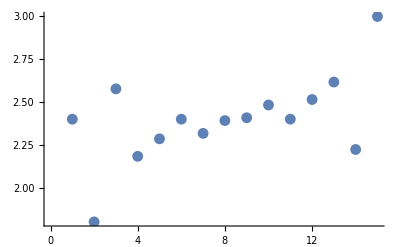

```mathematica
ListPlot[%]
```

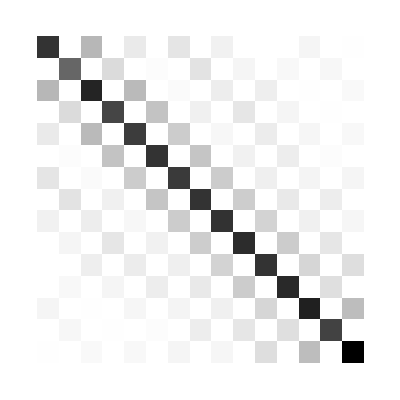

```mathematica
ArrayPlot[%]
```

```mathematica
ListPlot3D[V[100].Dg[100,10].Transpose[V[100]],PlotRange->Full]
```

-Graphics3D-

The diagonal V.,D_g.V^T seems to average the values of c

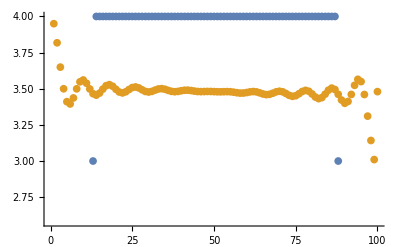

```mathematica
ListPlot[{Reverse[Diagonal[Dg[100,10]]],Reverse[Diagonal[V[100].Dg[100,10].Transpose[V[100]]]]}]
```

```mathematica
vdv[N_,g_]:=V[N].Dg[N,g].Transpose[V[N]]
Λ[N_]:=SparseArray[{{i_,j_}:>4*(Sin[((i-1)*π)/(2*N)])^2/;i==j},{N,N}]
```

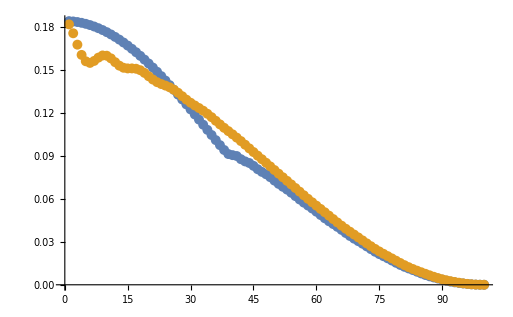

```mathematica
ListPlot[{Eigenvalues[X[100,10]],Reverse[Diagonal[1/(100-10-3)*DiagonalMatrix[Diagonal[vdv[100,10]]].Λ[100]]]}]
```